```mathematica
FactorBin[n_]:=FactorBin[n]= FactorInteger[Binomial[2 n, n]]
```

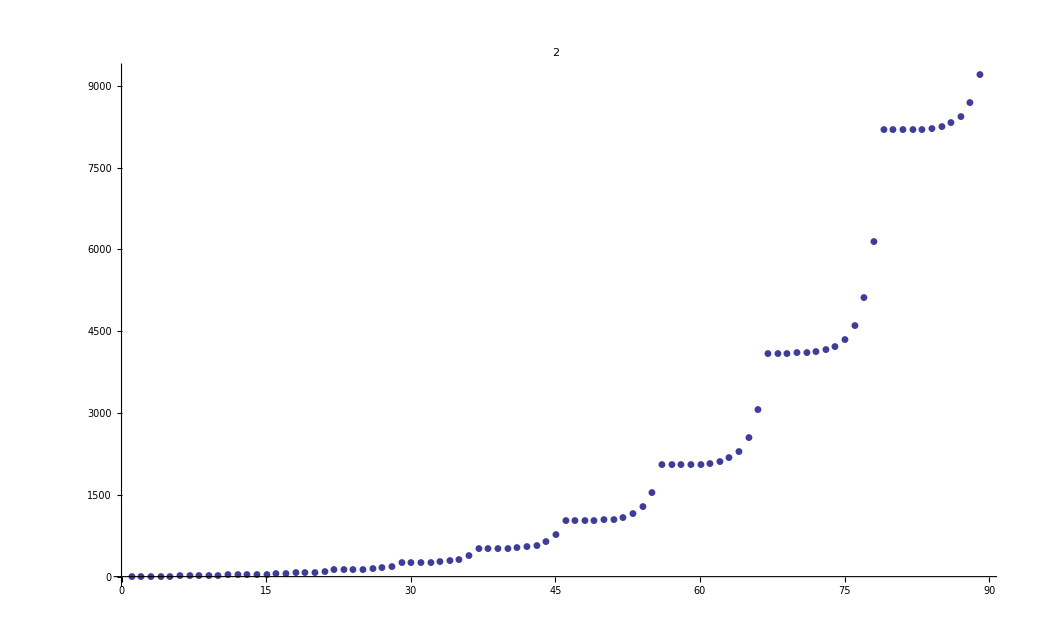

```mathematica
With[
{p = 2, exp=2, range=10000},
ListPlot[Map[Tooltip[#[[1]],#[[1]]]&,Select[Flatten[Table[Map[{n,#[[1]],#[[2]]}&,FactorBin[n]],{n,1,range}],1],#[[3]]==exp && #[[2]]==p&]], 
PlotLabel->p, 
Joined->p==2 && exp==1, 
PlotMarkers->Automatic,
PlotRange->All]
]
```

```mathematica
Table[
Length[
With[
{p = 2,  range=3000},
Map[IntegerDigits[#[[1]],p]&,Select[Flatten[Table[Map[{n,#[[1]],#[[2]]}&,FactorBin[n]],{n,1,range}],1],#[[3]]==exp && #[[2]]==p&]]
]
]
, {exp,1,10}
]
```

{12,65,210,450,671,708,525,262,82,14}

```mathematica
Ceiling[N[Log[2,3000]] ]/3
```

4

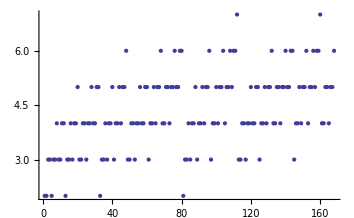

```mathematica
ListPlot[Map[Sum[n,{n,#}]&,%]]
```